## Question 1

```mathematica
exponentialGrowthRate[n_,r_]:=r*n
```

```mathematica
logisticGrowthRate[n_,r_,k_]:=r*n*(1-n/k)
```

```mathematica
alleeGrowthRate[n_,u_,v_,c_]:=((u*n)/(v+n)-c*n)n
```

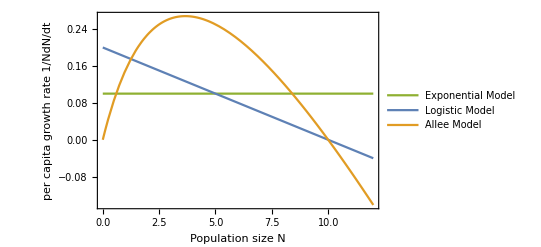

```mathematica
Plot[{1/x*exponentialGrowthRate[x,0.1],1/x*logisticGrowthRate[x,0.2,10],1/x*alleeGrowthRate[x,1.5,5,0.1]},{x,0,12},Frame->True,FrameLabel->{Style["Population size N",15],Style["per capita growth rate 1/NdN/dt",15]},PlotLegends->{"Exponential Model","Logistic Model", "Allee Model" },PlotStyle->ColorData[97,"ColorList"][[{3,1,2}]]]
```

## Question 2

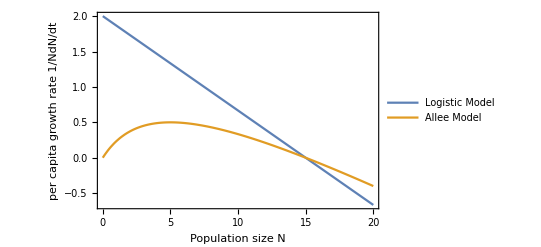

```mathematica
Plot[{1/n*logisticGrowthRate[n,2,15],1/n*alleeGrowthRate[n,2,5,0.1]},{n,0,20},Frame->True,FrameLabel->{Style["Population size N",15],Style["per capita growth rate 1/NdN/dt",15]},PlotLegends->{"Logistic Model", "Allee Model"}]
```

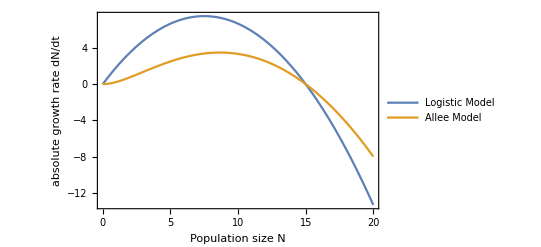

```mathematica
Plot[{logisticGrowthRate[n,2,15],alleeGrowthRate[n,2,5,0.1]},{n,0,20},Frame->True,FrameLabel->{Style["Population size N",15],Style["absolute growth rate dN/dt",15]},PlotLegends->{"Logistic Model", "Allee Model"}]
```

Finding

```mathematica
Solve[D[logisticGrowthRate[n,2,15],n]==0]
```

{{n→15/2}}

```mathematica
logisticGrowthRate[7.5,2,15]//N
```

7.5

```mathematica
Solve[D[alleeGrowthRate[n,2,5,0.1],n]==0&&n>0,n]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→8.66025}}

```mathematica
alleeGrowthRate[8.66025,2,5,0.1]
```

3.48076

```mathematica
Solve[D[1/n*alleeGrowthRate[n,2,5,0.1],n]==0&&n>0,n]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→5.}}

```mathematica
1/5*alleeGrowthRate[5,2,5,0.1]
```

0.5

## Question 3

Ricker Model

Find N^* candidates

```mathematica
Solve[n==r*n*Exp[-b*n],n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→0},{n→-Log[1/r]/b}}

```mathematica
ClearAll[f]
```

```mathematica
f[0]:=N0;
```

```mathematica
f[n_]:=r*f[n-1]*Exp[-b*f[n-1]]
```

```mathematica
f[2]
```

ⅇ^(-b N0-b ⅇ^(-b N0) N0 r) N0 r^2

```mathematica
D[f[1],N0]
```

Try the first fixed point

```mathematica
ⅇ^(-b N0) r-b ⅇ^(-b N0) N0 r/.N0->0
```

r

```mathematica
ⅇ^(-b N0) r-b ⅇ^(-b N0) N0 r/.N0->-Log[1/r]/b
```

1+Log[1/r]

```mathematica
Solve[Abs[1+Log[1/r]]==1&&r>0,r]
```

{{r→1},{r→ⅇ^2}}

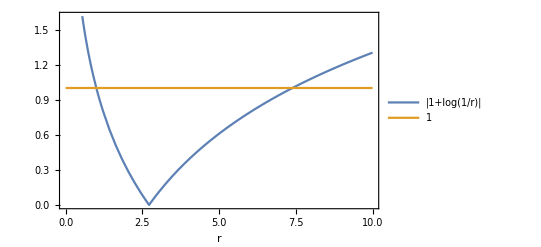

```mathematica
Plot[{Abs[1+Log[1/x]],1},{x,0,10},Frame->True,FrameLabel->{"r"},PlotLegends->{"|1+log(1/r)|","1"}]
```

Find the period-2 points

```mathematica
{{r->ⅇ^n},{r->-2/n ⅇ^n ProductLog[-n/(2 ⅇ^(n/2))]},{r->-2/n ⅇ^n ProductLog[n/(2 ⅇ^(n/2))]}}
```

```mathematica
Solve[With[{b=1},0==-n+r^2*n*Exp[-b*n*(1+r*Exp[-b*n])]]&&n>0,n]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[0==-n+ⅇ^(-n (1+ⅇ^-n r)) n r^2&&n>0,n]

```mathematica
Solve[FullSimplify[With[{b=1},0==-n+r^2*n*Exp[-b*n*(1+r*Exp[-b*n])]]&&n>0,Assumptions->{r∈Reals}],n,Reals,Assumptions->{r∈Reals}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^(n+ⅇ^-n n r) n==n r^2&&n>0,n,ℝ,Assumptions→{r∈ℝ}]

```mathematica
FullSimplify@With[{b=1},0==-n+r^2*n*Exp[-b*n*(1+r*Exp[-b*n])]]
```

n==ⅇ^(-n (1+ⅇ^-n r)) n r^2

```mathematica
Solve[n==ⅇ^(-b n (1+ⅇ^(-b n) r)) n r^2&&n>0,{n,r,b}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[n==ⅇ^(-b n (1+ⅇ^(-b n) r)) n r^2&&n>0,{n,r,b}]

```mathematica
Solve[With[{b=1,r=11},n==ⅇ^(-b n (1+ⅇ^(-b n) r)) n r^2&&n>0],{n}]
```

{{n→Root0.822Root[{-121+ⅇ^(#1+11 ⅇ^-#1 #1)&,0.821658539530982666}]0.8216585395309827},{n→Root2.40Root[{-121+ⅇ^(#1+11 ⅇ^-#1 #1)&,2.3978952727983705441}]2.3978952727983707},{n→Root3.97Root[{-121+ⅇ^(#1+11 ⅇ^-#1 #1)&,3.9741320060657584221}]3.9741320060657586}}

```mathematica
FullSimplify[n==r^2*n*Exp[-b*n*(1+r*Exp[-b*n])]]
```

n==ⅇ^(-b n (1+ⅇ^(-b n) r)) n r^2

```mathematica
Manipulate[Plot[{With[{b=1},r^2 n*Exp[-b*n*(1+r*Exp[-b*n])]],n},{n,0,10}],{r,0.1,100}]
```